Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Problemas de examen. Tema 12. Resolución numérica de ecuaciones no lineales. Problemas resueltos.

## Método de bisección

## 10.- Para aproximar las soluciones real de la ecuación x^3+x+1=0, considerar la función f(x) = x^3+x+1. ¿Es continua? ¿Es derivable? Evaluarla en -1 y 1. ¿Cuantas raíces tiene la ecuación? Aplicar el método de bisección 3 veces partiendo del intervalo [-1,1]. Enero 18

Solución:
La función f es continua en toda la recta real pues es un polinomio. También es derivable, pues es un polinomio. 
	f(-1)=-1-1+1=-1
	f(1)=1+1+1=3
Como el signo de la función f en -1 y en 1 son opuestos (siendo f continua; Teorema de Bolzano), la función se anula en algún punto entre -1 y 1. Por tanto, la ecuación tiene al menos una raíz. Para saber si tiene más, estudiamos la derivada de la función.
	f ’(x) = 3 x^2+1 
Vemos que la derivada de la función es siempre mayor que cero, la función es siempre estrictamente creciente y no puede tener más de un cero. Por tanto, hay una única solución de la ecuación y está entre -1 y 1.

Aplicamos ahora el método de bisección. Partimos del intervalo [-1,1] donde la función, que es continua, presenta cambio de signo y tiene por tanto una raíz.
	a_0= -1, b_0= 1, m_0= (a_0+b_0)/2= 0, f(a_0)=-1, f(b_0)=3, f(m_0)=1
Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_1= -1, b_1= 0, m_1= (a_1+b_1)/2= -1/2, f(a_1)=-1, f(b_1)=1, f(m_1)=(-1/2)^3+(-1/2)+1=(-1/8)-(1/2)+1>0

Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_2= -1, b_2= -1/2, m_2= (a_2+b_2)/2= -3/4, f(a_2)=-1, f(b_2)>0, f(m_2)=(-3/4)^3+(-3/4)+1=(-27/64)-(3/4)+1= (-27/64)-(48/64)+1=(-75/64)+1<0.
Como en el punto medio la función tiene el mismo signo que en el extremo de la izquierda, reducimos el intervalo por esa parte.
Tras tres pasos por el método de bisección hemos llegado a que la solución de la ecuación está en el intervalo [-3/4,-1/2].

## 10.- Estudiar los intervalos de el crecimiento de la función f(x) = x^3+2x+1. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Enero 21

Solución: La función f(x) = x^3+2x+1 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, en los puntos propuestos -1 y 1.
f(-1)= -1-2+1=-2 <0
f(1)=1+2+1 = 4>0
Hay un cambio de signo, y por el teorema de  Bolzano, hay al menos un cero. Por tanto, concluimos que hay un solo cero, y que está entre -1 y 1.
Para aplicar el método de bisección, consideramos el punto medio del intervalo m= (-1+1)/2=0. 
Evaluamos en el punto medio, f(0)=1>0. Por tanto, el cambio de signo se produce en el intervalo [-1,0].
Volvemos a aplicar el método de bisección, m= (-1+0)/2=-1/2. Evaluamos f(-1/2)=(-1/2)^3+2(-1/2)+1 = - 1/8 <0.
El cero de la funcion debe estar en el intervalo [-1/2,0].

## 10.- Estudiar los intervalos de crecimiento de la función f(x) = x^3+2x+2. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Febrero 21

Solución: La función f(x) = x^3+2x+2 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, en los puntos propuestos -1 y 1.
f(-1)= -1-2+2=-1 <0
f(1)=1+2+2 = 5>0
Hay un cambio de signo, y por el teorema de  Bolzano, hay al menos un cero. Por tanto, concluimos que hay un solo cero, y que está entre -1 y 1.
Para aplicar el método de bisección, consideramos el punto medio del intervalo m= (-1+1)/2=0. 
Evaluamos en el punto medio, f(0)=2>0. Por tanto, el cambio de signo se produce en el intervalo [-1,0].
Volvemos a aplicar el método de bisección, m= (-1+0)/2=-1/2. Evaluamos f(-1/2)=(-1/2)^3+2(-1/2)+2 = 7/8 >0.
El cero de la función debe estar en el intervalo [-1,-1/2].

## 10.- Estudiar los intervalos de el crecimiento de la función f(x) = x^3+2x-3. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Junio 21

Solución:
La función f(x) = x^3+2x-3 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función es  estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, si evaluamos en los puntos 0 y 2, obtenemos
f(0)=-3 <0
f(2)=8+4-3>0
Al haber cambio de signo, y la función continua en el intervalo [0,2], el teorema de  Bolzano nos dice que habrá al menos un punto donde se anula. Como es estrictamente creciente, como mucho hay un cero. Por tanto, f tiene un único cero y la ecuación  x^3+2x-3 =0 tiene una única solución.

Si evaluamos en los puntos propuestos -1 y 1.
f(-1)= -1-2-3 = -6 <0
f(1)=1+2-3 = 0
En el punto 1 hay un cero. Dado que la función es estrictamente creciente, solo tiene un cero.

Si quisiéramos aplicar el método de bisección para aproximar la solución de f(x)=0 partiendo del intervalo [-1,1], seguiríamos los siguientes pasos:
1) Se trata de una función continua en este intervalo (los polinomios están definidos y son funciones continuas en todo punto).
2) Comprobamos si hay cambio de signo en el intervalo inicial. Para ello evaluamos en los extremos:
	f(-1)=-6<0
	f(1)=0
Dado que en uno de los extremos del intervalo elegido la función se anula, hemos encontrado una solución de la ecuación 0 = x^3+2x-3, x=1.

Para utilizar el método de bisección necesitamos un intervalo donde se produzca cambio de signo de la función en los extremos.

## 11.- Dada la función f(x) = x^3+2x+1, ¿cuántas soluciones reales tiene exactamente la ecuación f(x)=0? Considerando el intervalo [-1,0] estudiar si podemos emplear el método de bisección para aproximar una solución de la ecuación f(x)=0 y, en caso afirmativo, realizar 3 divisiones del intervalo para aproximar la solución. Julio 22

Solución:
La función f es un polinomio, por tanto continua y derivable cuantas veces deseemos en toda la recta real. Además es un polinomio de grado impar, esto hace que tenga al menos una raíz (evaluando en números suficientemente grandes positivos y negativos, encontramos valores de distinto signo).
Por ejemplo, f(-2)= -8-4+1 <0, f(2) = 8+4+1 >0. Como f es una función continua en todo R, al cambiar de signo entre el -2 y el 2, el teorema de Bolzano nos dice que la función debe anularse en algún punto entre -2 y 2. 
La ecuación f(x)=0 tiene al menos una solución.

Para saber si hay más estudiamos la derivada de la función. f ’(x) = 3 x^2+2. La derivada es siempre positiva y nunca se anula, por tanto, por el teorema de Rolle, la función no puede anularse en dos puntos (pues si lo hiciese, la derivada debería anularse en un punto intermedio. Lo que no ocurre.)

La ecuación f(x)=0 tiene una única solución. 
Consideremos el intervalo [-1,0]. Veamos si podemos aplicar el método de bisección.
1) la función f es continua en [-1,0] (de hecho es continua en todo R).
2) la función cambia de signo en el intervalo [-1,0], f(-1)=-1-2+1<0, f(0)=1>0.
Podemos aplicar el método de bisección en el intervalo [-1,0].
a0=-1, b0=0, m0 = (a0+b0)/2 = -1/2, f(-1/2) = -1/8 -1+1<0. Por tanto, tenemos cambio de signo en el intervalo [-1/2,0].
a1=-1/2, b1=0, m1=(a1+b1)/2 = -1/4, f(-1/4)= -1/64-2/4+1 >0. Por tanto, tenemos cambio de signo en el intervalo [-1/2,-1/4].
a2=-1/2, b2=-1/4, m2= (a2+b2)/2=(-1/2-1/4)/2=-3/8, f(-3/8)= -27/512 - 6/8 + 1 = (-27-384+512)/512 >0. Por tanto, tenemos un cambio de signo en el intervalo [-1/2,-3/8].

## 11.- Dada la función f(x) = x^3+2x-2, utilizar el método de bisección para aproximar la solución de la ecuación x^3+2x-2=0, buscando un intervalo donde la función sea continua y tenga cambio de signo, y realizando dos subdivisiones dicho intervalo por el método de bisección. Julio 24

Solución:
La función f es un polinomio, por tanto continua y derivable cuantas veces deseemos en toda la recta real. Además es un polinomio de grado impar, esto hace que tenga al menos una raíz (evaluando en números suficientemente grandes, positivos y negativos, encontramos valores de distinto signo).
Por ejemplo, f(-2)= -8-4-2 <0, f(2) = 8+4-2 >0. Como f es una función continua en todo R, al cambiar de signo entre el -2 y el 2, el teorema de Bolzano nos dice que la función debe anularse en algún punto entre -2 y 2. 
La ecuación f(x)=0 tiene al menos una solución en el intervalo [-2,2].

Consideremos el intervalo [-2,2]. Veamos si podemos aplicar el método de bisección.
1) la función f es continua en [-2,2] (de hecho es continua en todo R).
2) la función cambia de signo en el intervalo [-2,2], f(-2)<0, f(2)>0.
Podemos aplicar el método de bisección en el intervalo [-2,2].
a0=-2, b0=2, m0 = (a0+b0)/2 = 0, f(0) = -2<0. Por tanto, tenemos cambio de signo en el intervalo [0,2].
a1=0, b1=2, m1=(a1+b1)/2 = 1, f(1)= 1+2-2 >0. Por tanto, tenemos cambio de signo en el intervalo [0,1].
a2=0, b2=1, m2= (a2+b2)/2=(0+1)/2=1/2, f(1/2)=1/8+1-2=-7/8<0. Por tanto, tenemos un cambio de signo en el intervalo [1/2,1].

## Método de Newton

## 10.- Aproximar una solución de la ecuación x^2-2=0, aplicando el método de Newton a la función f(x) = x^2-2, con punto inicial x_0=1 y haciendo dos iteraciones. Octubre 18, Julio 18

Solución:
f(x)=x^2-2, x_(n+1)= x_n -f(x_n)/f’(x_n) = x_n-(x_n^2-2)/(2 x_n), 
x_0=1,
x_1= x_0-(x_0^2-2)/(2 x_0) = 1-(1^2-2)/(2*1) = 1-(-1)/2 = 3/2
x_2=x_1-(x_1^2-2)/(2 x_1) = (3/2)-((3/2)^2-2)/(2*(3/2))=3/2-(1/4)/3=3/2-1/12=17/12
Con el Mathematica

```mathematica
f[x_]:=x^2-2
```

```mathematica
x0=1;
```

```mathematica
x1=x0-f[x0]/f'[x0]
```

3/2

```mathematica
x2=x1-f[x1]/f'[x1]
```

17/12

## 9.- Para aproximar una solución real de la ecuación x^3-2x-1=0 realizar tres iteraciones del método de Newton-Raphson partiendo del valor inicial x_0=0. Enero 20

Solución:
f(x)=x^3-2x-1, x_(n+1)= x_n -f(x_n)/f’(x_n) = x_n-(x_n^3-2 x_n-1)/(3 x_n^2-2), 
x_0=0,
x_1= x_0-(x_0^3-2 x_0-1)/(3 x_0^2-2) =1/(-2) = -1/2
x_2=x_1-(x_1^3-2 x_1-1)/(3 x_1^2-2) = -1/2-(-1/8+1-1)/(3/4-2)=-1/2-(-1/8)/(-5/4)=-1/2-1/10=-6/10=-3/5
x_3=-3/5-(-27/125+6/5-1)/(3*9/25-2) =-3/5-(-27/125+150/125-125/125)/(135/125-250/125) =-3/5-(2/115)=-71/115

## 11.- Dada la función f(x) = x^3+2x-1, ¿cuántas soluciones tiene la ecuación f(x)=0? Comenzando con el valor aproximado x_0=0, calcular dos aproximaciones a una solución utilizando el método de Newton para resolver ecuaciones no lineales. Enero 22

Solución: 
La función f es polinómica. Por tanto, f es continua y derivable cuantas veces queramos en toda la recta real. Al ser de grado impar, toma signos opuestos al tender x a más  o menos infinito. En concreto, al tener el coeficiente líder positivo, cuando x → +∞, f(x) → +∞, mientras que cuando x → -∞, f(x) → -∞. De aquí obtenemos que f tomará valores positivos y valores negativos, y utilizando el teorema de Bolzano sabremos que f debe anularse en algún punto. Es decir, la ecuación f(x)=0 tiene al menos una solución. Para saber si hay más consideramos la derivada de la función f’(x)= 3 x^2+2 es siempre positiva y mayor que cero, por tanto f(x) será una función estrictamente creciente y no podrá anularse en más de un punto.

La ecuación f(x)= x^3+2x-1=0 tiene una sola solución.

Vamos a aplicar el método de Newton para aproximar las raíces de una ecuación comenzando con la aproximación inicial x_0=0.
El método de Newton, partiendo de una aproximación inicial, y considerando las rectas tangentes a la gráfica de la función, y los puntos donde las tangentes se anulan, va generando una sucesión de aproximaciones que se espera converja a un cero de la función. En concreto, los valores se obtienen mediante la fórmula:
x_(n+1)=x_n- f(x_n)/f'(x_n).

En nuestro caso, 
x_0=0, 
x_1=x_0- f(x_0)/f'(x_0) = 0- f(0)/f'(0) = - (-1)/2= 1/2
x_2=x_1- f(x_1)/f'(x_1) = 1/2 - f(1/2)/f'(1/2) = 1/2 - ((1/2)^3+2(1/2)-1)/(3(1/2)^2+2) = 1/2 - (1/8+1-1)/(3/4+2) = 1/2 - (1/8)/(11/4) = 1/2 - 1/22 = 10/22 = 5/11.

Con el Mathematica:

```mathematica
f[x_]:=x^3+2x-1
```

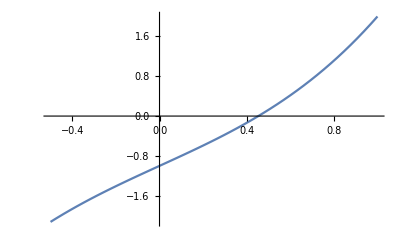

```mathematica
Plot[f[x],{x,-1/2,1}]
```

```mathematica
x0=0;x1=x0-f[x0]/f'[x0];x2=x1-f[x1]/f'[x1];{x0,x1,x2}
```

{0,1/2,5/11}

## 11.- Para calcular la raíz cúbica de dos, consideramos la función f(x)= x^3-2, y aplicamos el método de Newton para resolver ecuaciones no lineales comenzando con el valor inicial x_0=2. Calcular las dos siguientes aproximaciones utilizando el método de Newton. Enero 23

Solución: 
La función f es polinómica. Por tanto, f es continua y derivable cuantas veces queramos en toda la recta real. Vamos a aplicar el método de Newton para aproximar las raíces de una ecuación comenzando con la aproximación inicial x_0=2.
El método de Newton, partiendo de una aproximación inicial, y considerando las rectas tangentes a la gráfica de la función, y los puntos donde las tangentes se anulan, va generando una sucesión de aproximaciones que se espera converja a un cero de la función. En concreto, los valores se obtienen mediante la fórmula:
x_(n+1)=x_n- f(x_n)/f'(x_n).

En nuestro caso, 
x_0=2, 
f(x) = x^3-2
f ’(x) = 3 x^2

x_1=x_0- f(x_0)/f'(x_0) = 2- f(2)/f'(2) = 2- 6/12= 3/2
x_2=x_1- f(x_1)/f'(x_1) = 3/2 - f(3/2)/f'(3/2) = 3/2 - ((3/2)^3-2)/(3(3/2)^2) = 3/2 - (11/8)/(27/4) = 3/2 - 11/54=81/54-11/54=70/54=35/27.

Con el Mathematica:

```mathematica
f[x_]:=x^3-2
```

```mathematica
x0=2;x1=x0-f[x0]/f'[x0];x2=x1-f[x1]/f'[x1];{x0,x1,x2}
```

{2,3/2,35/27}

## 11.- Utilizar el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 realizando dos iteraciones a partir del punto x_0 =0, con f(x)=x^3+x+1. Enero 24

Solución:
El método de Newton, partiendo de una aproximación inicial, y considerando las rectas tangentes a la gráfica de la función, y los puntos donde las tangentes se anulan, va generando una sucesión de aproximaciones que se espera converja a un cero de la función. En concreto, los valores se obtienen mediante la fórmula:
x_(n+1)=x_n- f(x_n)/f'(x_n).

En nuestro caso, 
x_0=0, 
f(x) = x^3+x+1
f ‘(x) = 3 x^2+1

x_1=x_0- f(x_0)/f'(x_0) = 0- f(0)/f'(0) = - 1/1=-1
x_2=x_1- f(x_1)/f'(x_1) = -1 - f(-1)/f'(-1) = -1 - ((-1)^3+(-1)+1)/(3(-1)^2+1) = -1 - (-1)/4 = -3/4.

Con el Mathematica:

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x0=0;x1=x0-f[x0]/f'[x0];x2=x1-f[x1]/f'[x1];{x0,x1,x2}
```

{0,-1,-3/4}

## Aula de Informática

## 3.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3 + x +1 = 0 partiendo de x_0=0. El séptimo decimal de x_5 es: 1) 7, 2) 8, 3) 6, 4) 2, 5) 4 El sexto decimal de x_5 es: 1) 7, 2) 8, 3) 6, 4) 2, 5) 4 Enero 24. Aula de Informática

Solución: Dada la función f(x) = x^3 + x +1, y partiendo de x_0=0, calculamos las sucesivas iteraciones del método de Newton con la fórmula x_(n+1)= x_n - f(x_n)/ f ’(x_n).

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x0=0;
```

```mathematica
x1=x0-f[x0]/f'[x0];
```

```mathematica
x2=x1-f[x1]/f'[x1];
```

```mathematica
x3=x2-f[x2]/f'[x2];
```

```mathematica
x4=x3-f[x3]/f'[x3];
```

```mathematica
x5=x4-f[x4]/f'[x4];
```

```mathematica
N[x5,10]
```

-0.6823278039

El séptimo decimal de x_5 es el 8. El sexto decimal de x_5 es el 7.

## 4.- Realizar cuatro iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x -2=0 partiendo de x_0=0. El valor de x_4 con 10 cifras decimales es: 1) 0.3393167250, 2) 0.4988619908, 3) 0.5652441238, 4) 0.6443318729, 5) 0.8575419966 Enero 22. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]-2
```

```mathematica
s=0;Do[s=s-f[s]/f'[s],{4}];Print["Una aproximación sería ",N[s,10]]
```

Una aproximación sería 0.4988619908

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x+1=0 partiendo de x_0=-2. Escribir valor de x_5 con 10 cifras decimales: Febrero 21. Aula de Informática.

```mathematica
x0=-2;
```

```mathematica
h[x_]:=x^3+2x+1
```

```mathematica
x1=x0-h[x0]/h'[x0]
```

-17/14

```mathematica
x2=x1-h[x1]/h'[x1]
```

-6285/8813

```mathematica
x3=x2-h[x2]/h'[x2]
```

-1181027022047/2413366135369

```mathematica
x4=x3-h[x3]/h'[x3]
```

-17350907135779988805460449109686244055/38211180030994919512515279408659263181

```mathematica
N[x5,20]
```

-0.4533978931376927114

```mathematica
x5=x4-h[x4]/h'[x4]
```

-(66239044616239855126316915726128640907368903089545413824501563678964999425360538850844095374347564515986327291491/146094734048805284309751253526702576567995747072754084953619010306042489581229845704427375937139418385247212205057)

```mathematica
N[%,20]
```

-0.4533978931376927114

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 21. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cuatro iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x+1=0 partiendo de x_0=-2. El valor de x_4 con 10 cifras decimales es: 1) -0.4540793328, 2) 0.4540792113, 3) -0.4540790157, 4) -0.4540796425, 5) -0.4540792217 Enero 21. Aula de Informática.

```mathematica
f[x_]:=x^3+2x+1
```

```mathematica
x0=-2;
```

```mathematica
x1=x0-f[x0]/f'[x0];
```

```mathematica
x2=x1-f[x1]/f'[x1];
```

```mathematica
x3=x2-f[x2]/f'[x2];
```

```mathematica
x4=x3-f[x3]/f'[x3];
```

```mathematica
N[x4,20]
```

-0.45407933284724094968

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación 8 x^2 - 9x + cos x=0 partiendo de x_0= -1, x_1=1/2. Escribir x_5 con 7 cifras decimales. Enero 20. Aula de Informática.

x_5= 0.141898529575

```mathematica
f[x_]:=8x^2-9x+Cos[x]
```

```mathematica
x0=-1; x1=1/2;
```

```mathematica
x2=x1-f[x1](x1-x0)/(f[x1]-f[x0]);
```

```mathematica
x3=x2-f[x2](x2-x1)/(f[x2]-f[x1]);
```

```mathematica
x4=x3-f[x3](x3-x2)/(f[x3]-f[x2]);
```

```mathematica
x5=x4-f[x4](x4-x3)/(f[x4]-f[x3]);
```

```mathematica
N[x5,12]
```

0.141898529575

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación 8 x^2 - 9x + cos x=0 partiendo de x_0=1/2, x_1=2. Escribir x_5 con 7 cifras decimales. Enero 20. Aula de Informática.

```mathematica
f[x_]:=8x^2-9x+Cos[x]
```

```mathematica
x0=1/2; x1=2;
```

```mathematica
x2=x1-f[x1](x1-x0)/(f[x1]-f[x0]);
```

```mathematica
x3=x2-f[x2](x2-x1)/(f[x2]-f[x1]);
```

```mathematica
x4=x3-f[x3](x3-x2)/(f[x3]-f[x2]);
```

```mathematica
x5=x4-f[x4](x4-x3)/(f[x4]-f[x3]);
```

```mathematica
N[x5,12]
```

0.970644695525

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x=0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución: Siguiendo la práctica de ecuaciones no lineales:

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,15],". La función vale ",N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximación sería -0.419659987913863. La función vale -6.56047157627×10^-7

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + sen x +1 =0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución: Siguiendo la práctica de ecuaciones no lineales:

```mathematica
f[x_]:=x^3+2x+Sin[x]+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.12327545921

-0.54987916884

-0.340125668858

-0.323952953512

-0.323885621116

Una aproximación sería -0.323885621116. La función vale -3.68424462046×10^-9

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19.Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x=0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución:
Siguiendo la práctica de ecuaciones no lineales:

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximación sería -0.419659987914. La función vale -6.56047157627×10^-7

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + sen x +1 =0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución:
Siguiendo la práctica de ecuaciones no lineales:

```mathematica
f[x_]:=x^3+2x+Sin[x]+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.12327545921

-0.54987916884

-0.340125668858

-0.323952953512

-0.323885621116

Una aproximación sería -0.323885621116. La función vale -3.68424462046×10^-9

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+M=0 partiendo de x_0=N. Escribir x_5 con 10 cifras decimales. x_5= Junio 18. Aula de Informática

```mathematica
Clear[ff]
```

```mathematica
m=7;n=2;
```

```mathematica
ff[x_]:=x^3+x+m
```

```mathematica
s=n;
Do[s=s-ff[s]/ff'[s];Print[N[s,15]],{5}];Print["Una aproximación sería ",N[s,15],". La función vale ",N[ff[s],10]]
```

0.692307692307692

-2.59914115011202

-1.98043732078654

-1.76518676095496

-1.73954766382636

Una aproximación sería -1.73954766382636. La función vale -0.00346425279

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x_0=-2. Escribir x_5 con 20 cifras decimales. x_5= Enero 18. Aula de Informática.

Solución:
Seguimos lo que aparece en la Práctica de ECUACIONES NO LINEALES.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,20]],{5}];Print["Una aproximación sería ",N[x,20],". La función vale ",N[f[x],15]]
```

-1.3076923076923076923

-0.89270864270864270864

-0.71453940099213945862

-0.68319313870858675011

-0.68232844296175089986

Una aproximación sería -0.68232844296175089986. La función vale -1.53182140397554×10^-6

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x_0=-3. Escribir x_5 con 20 cifras decimales. x_5= Enero 18. Aula de Informática.

Solución: Seguimos lo visto en prácticas.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x=-3;
Do[x=x-f[x]/f'[x];Print[N[x,20]],{5}];Print["Una aproximación sería ",N[x,20],". La función vale ",N[f[x],15]]
```

-1.9642857142857142857

-1.2849100894034457276

-0.88069436473689815233

-0.71123142294341466255

-0.68302625360238314179

Una aproximación sería -0.68302625360238314179. La función vale -0.00167498306484417